#### Graphs for 12/01/17

Problem 9.4.18

```mathematica
Manipulate[Plot[{y=1-x,y=(0.75-.5*x)/a},{x,0,5},PlotRange->{{0,5},{0,5}}],{a,0,6}]
```

Part D

```mathematica
Clear[a]
```

```mathematica
f[x_,y_]:={{1-2*x-y,-x},{-0.5*y,.75-2*a*y-0.5*x}}
```

```mathematica
f[0,0]
```

```mathematica
Eigenvalues[{{1,0},{0.,0.75}}]
```

{1.,0.75}

```mathematica
f[1,0]
```

```mathematica
Eigenvalues[{{-1,-1},{0.,0.25}}]
```

{-1.,0.25}

```mathematica
f[0,0.75/a]
```

```mathematica
Eigenvalues[{{1-0.75/a,0},{-0.375/a,-0.75}}]
```

{-0.75,(1. (-0.75+1. a))/a}

```mathematica
f[1-(1/(4*a-2)),1/(4*a-2)]
```

f[1-1/(-2+4 a),1/(-2+4 a)]

```mathematica
Eigenvalues[{{1-1/(-2+4 a)-2 (1-1/(-2+4 a)),-1+1/(-2+4 a)},{-0.5/(-2+4 a),0.75-(2 a)/(-2+4 a)-0.5 (1-1/(-2+4 a))}}]
```

Part F

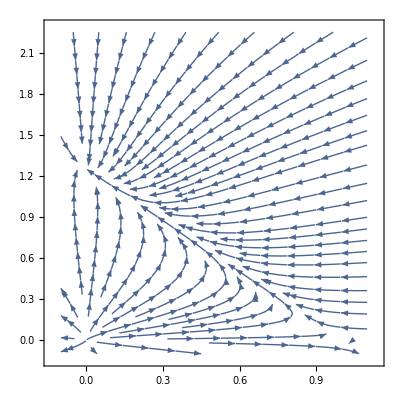

```mathematica
StreamPlot[{x*(1-x-y),y*(0.75-0.6*y-0.5*x)},{x,-.1,1.1},{y,-.1,(0.75/.6)+1}]
```

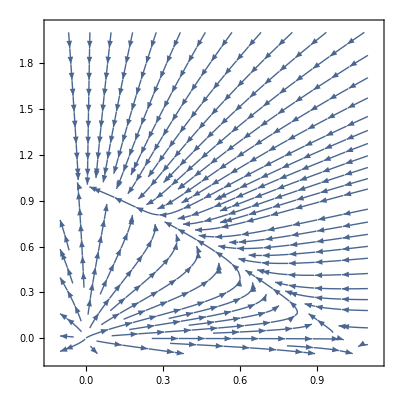

```mathematica
StreamPlot[{x*(1-x-y),y*(0.75-0.75*y-0.5*x)},{x,-.1,1.1},{y,-.1,(0.75/.75)+1}]
```

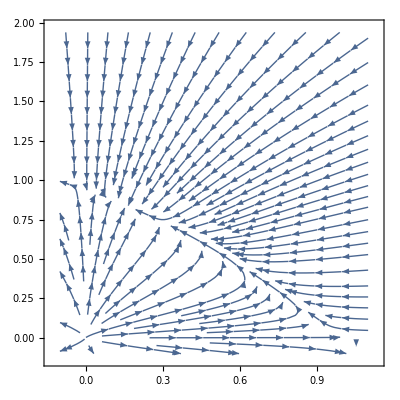

```mathematica
StreamPlot[{x*(1-x-y),y*(0.75-0.8*y-0.5*x)},{x,-.1,1.1},{y,-.1,(0.75/.8)+1}]
```

#### Problem 9.5.2

Part A

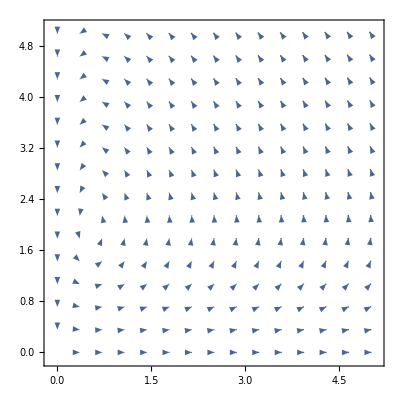

```mathematica
VectorPlot[{x*(1-.5*y),y*(.5*x-.25)},{x,0,5},{y,0,5},VectorScale->{0.01,5}]
```

Part D

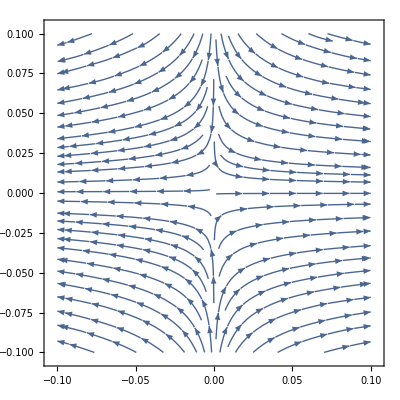

```mathematica
StreamPlot[{x*(1-.5*y),y*(.5*x-.25)},{x,-.1,.1},{y,-.1,.1}]
```

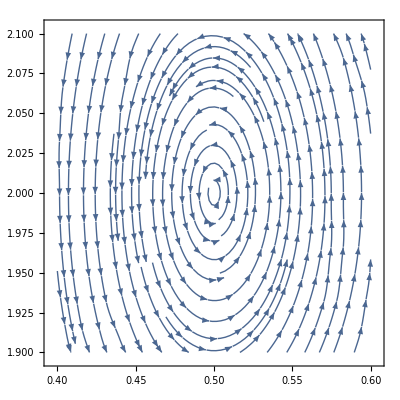

```mathematica
StreamPlot[{x*(1-.5*y),y*(.5*x-.25)},{x,.4,.6},{y,1.9,2.1}]
```

Part E

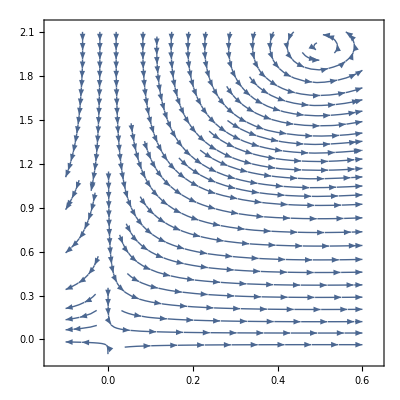

```mathematica
StreamPlot[{x*(1-.5*y),y*(.5*x-.25)},{x,-.1,.6},{y,-.1,2.1}]
```

#### Problem 9.5.9

```mathematica
Period of Oscillation will be 2*Pi/Sqrt(a*b)
```

Part A

```mathematica
g[a_,b_,x_,y_]:={{a-(a*y/2),-a*x/2},{b*y/3,(b*x/3)-b}}
```

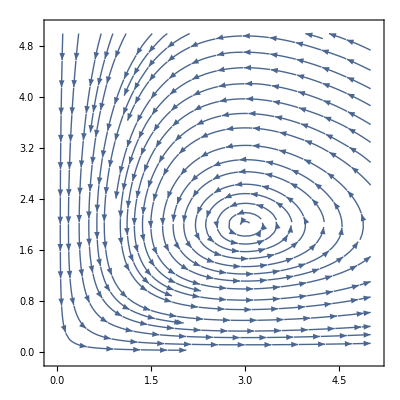

```mathematica
StreamPlot[{1*x*(1-(y/2)),1*y*((x/3)-1)},{x,0,5},{y,0,5}]
```

T=2*pi ~ 6.28

Part B

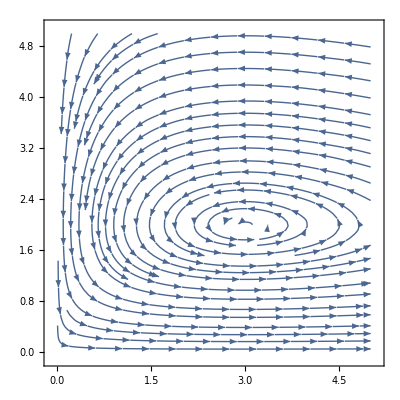

```mathematica
StreamPlot[{3*x*(1-(y/2)),1*y*((x/3)-1)},{x,0,5},{y,0,5}]
```

T=2*pi/sqrt(3) ~3.63

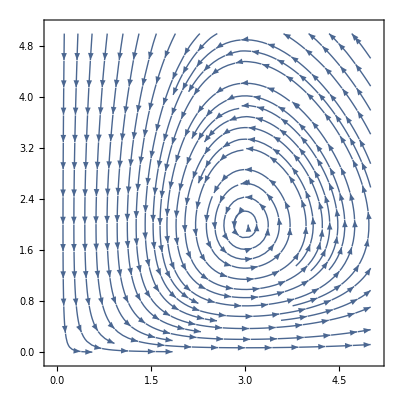

```mathematica
StreamPlot[{(1/3)*x*(1-(y/2)),1*y*((x/3)-1)},{x,0,5},{y,0,5}]
```

T=2*Pi*Sqrt(3) ~10.88

Part C

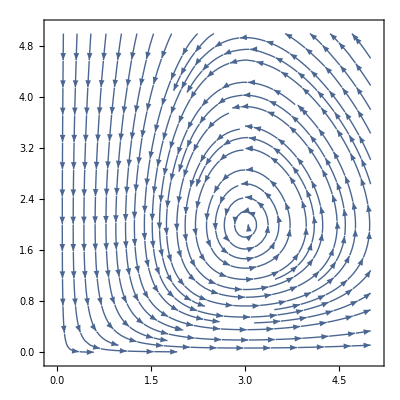

```mathematica
StreamPlot[{1*x*(1-(y/2)),3*y*((x/3)-1)},{x,0,5},{y,0,5}]
```

T=2*Pi/Sqrt(3) ~ 3.63

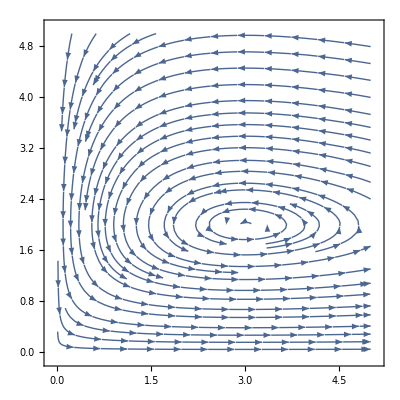

```mathematica
StreamPlot[{1*x*(1-(y/2)),(1/3)*y*((x/3)-1)},{x,0,5},{y,0,5}]
```

T=2*Pi*Sqrt(3) ~ 10.88

```mathematica
Solve[(l^2)-((a-3)/(4*a))*l+((9-12*a)/(16*a))==0,l]
```

{{l→-3/4},{l→(-3+4 a)/(4 a)}}